4

留数定理及其应用

我们终于走到这一步：

在孤立奇点的去心邻域，一个解析函数可以展开成Laurent级数，

这个Laurent级数是唯一的、在展开环域（去心邻域）是绝对收敛且内闭一致收敛的，

因而求导、求积与级数的求和可以交换次序。

从而对一般复变函数的积分，可望先展开为级数，再利用下式求积分。

∳_C ⅆz/(z-a)^n=2π ⅈ δ_(n,1)

具体如何做？有何应用？正是本章的内容。

## 4.1 留数定理

目标：利用级数展开，解决复变函数的闭合回路积分问题。

### 留数定理

由Cauchy定理，对一个闭合回路积分，

若闭合回路所包围的区域是解析的，那么积分为 0 ；

若回路内有一些奇点，那么积分值等于包围这些奇点的各闭回路积分值之和。

若这些奇点是孤立奇点，计算孤立奇点邻域一条闭合回路的积分就可用留数定理计算。

引理：设 z_0 是解析函数 f(z) 的一个孤立奇点，函数在 z_0 的去心邻域  D：0<|z-z_0|<δ （ z_0 为有限远点）或  R<|z|<∞ （ z_0 为无穷远点）内解析，则函数对 D 内任意一条包围 z_0 的闭合回路正向的积分

∳_(c:z_0) f(z)ⅆz=2π ⅈ  Res f(z_0)，

其中 c:z_0 为在 D 内包围 z_0 的任意一条闭合回路，Resf(z_0) 称为函数在 z_0的留数，“闭合回路积分残留下来的数”。

包围 z_0 的闭合回路正向：在回路上走，z_0 在左手边。

若 z_0 在有限区，则在区域 D：0<|z-z_0|<δ 内，

∳_(c:z_0) f(z)ⅆz=∳_(c:z_0) (∑_(k=-∞))^∞(a_k(z-z_0))^k ⅆz=(∑_(k=-∞))^∞a_k∳_(c:z_0) (z-z_0)^k ⅆz=2π ⅈ (∑_(k=-∞))^∞a_k δ_(k,-1)=2π ⅈ a_-1

Res f(z_0)=a_-1。 注意积分回路取向：对有限远点，回路正向应该是逆时针，留数为 a_-1。

若 z_0 为无穷远点，则在区域 D：R<|z|<∞ 内，（注意积分路径的走向）

∲_(c:∞) f(z)ⅆz=∲_(c:∞) (∑_(k=-∞))^∞a_k z^k ⅆz=(∑_(k=-∞))^∞a_k∲_(c:∞) z^k ⅆz=-2π ⅈ (∑_(k=-∞))^∞a_k δ_(k,-1)=-2π ⅈ a_-1

Res f(∞)=-a_-1。 注意积分回路取向：对无穷远点，回路正向应该是顺时针，留数为 -a_-1。

注意无穷远点的留数与有限远点的留数形式上差一个负号。

对有限远点，若 z_0 不是奇点（或是可去奇点），则 Res f(z_0)=0，对无限远点，即使它不是奇点，也有可能 Res f(z_0)≠0。

这是因为无穷远是否为奇点是看正幂次系数，而留数是 -a_-1   —— 负 1 幂次的系数

例如：f(z)=e^(1/z)在 z=∞点是可去奇点（极限有限），但 Res f(∞)=-1≠0。

留数定理：设区域 D 的边界  C 是分段光滑的闭合曲线，函数 f(z) 在 D 内除有限个孤立奇点  b_k, k=1,2,...,n 外单值解析，在 D̄ 上连续，且在  C 上无奇点，则

∳_C f(z)ⅆz=2π ⅈ (∑_(k=1))^n Res f(b_k)

这个定理实际上是复连通Cauchy 定理和上一个引理的直接结果。

如果函数 f(z) 在有限区域只有有限个孤立奇点，则包括无穷远点在内的所有奇点的留数和为 0。

取回路 C_R 包围所有有限远的奇点，则

∳_C_R f(z)ⅆz=2π ⅈ (∑_(k=1))^n Res f(b_k)

但:∳_C_R f(z)ⅆz=-∲_C_R f(z)ⅆz  ⟹^视为绕无穷远点的闭回路  -2ℼ ⅈ Resf(∞)

从而：(∑_(k=1))^n Res f(b_k)+Res f(∞)=0，特别注意即使无穷远点是可去奇点，其留数也可能不为 0。

### 留数的求法

留数：Laurent展开式中负一幂次项的系数 a_-1（对有限远点）或 -a_-1（对无穷远点），最直接的求法就是Laurent展开，当然还有其它简便方法。

有限区的单极点 b （一阶极点）

单极点：f(z)=(a_-1)/(z-b)+(∑_(k=0))^∞(a_k(z-b))^k         （仅有负 1 幂次）

⟹    (z-b) f(z)=a_-1+(z-b)(∑_(k=0))^∞(a_k(z-b))^k

两边同时求极限：Res f(b)=a_-1=lim_(z→b) (z-b)f(z)  （对单极点）

若 f(z)=(P(z))/(Q(z)) 且 P(b)≠0, Q(b)=0 为一阶 0 点，Q'(b)≠0，则

Res f(b)=lim_(z→b) (z-b)(P(z))/(Q(z))=lim_(z→b) (P(z))/((Q(z)-Q(b))/(z-b))=(lim_(z→b) P(z))/(lim_(z→b) (Q(z)-Q(b))/(z-b))=(P(b))/(Q'(b))

注：只有 Q'(b)≠0，此式才成立

但是，若 f(z)=(P(z))/(Q(z)) 且 P(b)=0 为 m 阶 0 点， Q(b)=0 为 m+1 阶 0 点（b 仍是单极点）

这时Q'(b)=0， Res f(b)≠ lim_(z→b) (P(z))/(Q'(z)) 再用洛必达法则

例：z=0是 f(z)=(sin z)/z^2 的单极点，

Res f(0)=lim_(z→0) z(sin z)/z^2=1,    利用了：a_-1=lim_(z→b) (z-b)f(z)

如果套用(BookChapterNumber.EquationNumbered)式，则：lim_(z→0) (sin z)/((z^2)')=lim_(z→0) (sin z)/(2z)=1/2≠Res f(0)=1

那么，此时上面的(BookChapterNumber.EquationNumbered)式为何不能用？（答：错在蓝色部分吗，商的极限不等于极限的商）

例题： 判断奇点及求留数时别忘了 ∞ 点

f(z)=1/(sin z)，z=0为单极点，Res f(0)=lim_(z→0) 1/((sin z)')=lim_(z→0) 1/(cos z)=1

z=∞ 为非孤立奇点，因为 z=2k π 可以落到任意的一个大圆之外。

f(z)=(ⅇ^z cos z+1)/(z^n-1)，z=1为单极点，Res f(1)=lim_(z→1) (ⅇ^z cos z+1)/((z^n-1)')=lim_(z→1) (ⅇ^z cos z+1)/(n z^(n-1))=(ⅇ cos 1+1)/n

z=∞ 为本性奇点。

有限区的 m 阶极点 b，m≥1

m 阶极点：f(z)=(a_-m(z-b))^-m+...+(a_-1(z-b))^-1+a_0+...，其中 a_-m≠0

⟹    (z-b)^mf(z)=a_-m+...+(a_-1(z-b))^(m-1)+(a_0(z-b))^m+...，其中 a_-m≠0

两边同时求 (m-1)阶导数并求极限

(m-1)! a_-1=lim_(z→b) (ⅆ^(m-1)[(z-b)^m f(z)])/(ⅆ z^(m-1))，  Res f(b)=a_-1

Res f(b)=1/((m-1)!)lim_(z→b) [(z-b)^(m^)f(z)]^(m-1)，  m=1时退化为单极点情况

例题：

f(z)=(ⅇ^z cos z-1)/z^5,   z=0为 4  阶极点

Res f(0)=(1/(3!)[z^4(ⅇ^z cos z-1)/z^5])^(3)

```mathematica
Clear["Global`*"]
f[z_]:=(ⅇ^z Cos[z]-1)/z^5;
f3=D[1/(3!)z^4 f[z],{z,3}];
Limit[f3,z->0]
Residue[f[z],{z,0}]
Series[f[z],{z,0,3}]
c[n_]:=SeriesCoefficient[f[z],{z,0,n}]
c[-1]
c[n]
```

-1/6

-1/6

1/z^4-1/(3 z^2)-1/(6 z)-1/30+z^2/630+z^3/2520+O[z]^4

-1/6

Piecewise[{{-((2-2 ⅈ) ((1-ⅈ)^n+ⅈ (1+ⅈ)^n))/((5+n)!), n>-5}, {0, True}}]

有限区的本性奇点 b：只能作Laurent展开求 a_-1。

无穷远点：即使是可去奇点，无穷远点的留数也可能不为 0，故求留数时一定别忘了计算 Res f(∞)

f(z)=(∑_(k=-∞))^∞a_k z^k， Res f(∞)=-a_-1，∲_(c:∞) f(z)ⅆz=2π ⅈ Res f(∞)=-2π ⅈ a_-1

做变换：ζ=1/z   ⟹    g(ζ)=-1/ζ^2f(1/ζ)， 在 ζ=0 去心邻域展开

g(ζ)=-(∑_(k=-∞))^∞a_-k ζ^(k-2)=-(∑_(k=-∞))^∞(...+(a_-1)/ζ+a_0/ζ^2+...)

故：f(z)在 z=∞ 的留数等于 g(ζ)=-1/ζ^2f(1/ζ)在 ζ=0的留数

Res f(∞)=Res g(0),    其中   g(ζ)=-1^/ζ_^2f(1/ζ)

例题：

1.  f(z)=(z+2ⅈ)/(z^5+4 z^3) ，求奇点及其留数 （所有的奇点及其留数）

奇点：多为分母 的零点（注意零点阶数），还有 ∞ 点（总把它视为奇点）

奇点：z=0,  三阶， Res f(0)=1/(2!)lim_(z→0) [(z+2ⅈ)/(z^2+4)]^(2)=-ⅈ/8

奇点：z=2ⅈ, 单极点，Res f(2ⅈ)=lim_(z→2ⅈ) (z+2ⅈ)/((z^5+4 z^3)')=ⅈ/8

奇点：z=-2ⅈ, 可去奇点，Res f(-2ⅈ)=0  （有限远点为可去奇点时，留数为 0 ）

奇点：z=∞, 可去奇点，但留数未必是 0  （无限远点为可去奇点时，留数可能非  0 ）

直接展开 f(z)=1/z^3 1/(z-2ⅈ)=1/z^4(∑_(k=0))^∞((2ⅈ)/z)^k，无负一幂次，Res f(∞)=0

```mathematica
Clear["Global`*"]
f[z_]:=(z+2ⅈ)/(z^5+4 z^3);
Residue[f[z],{z,0}]
Residue[f[z],{z,2ⅈ}]
Residue[f[z],{z,-2ⅈ}]
Residue[f[z],{z,∞}]
Residue[-1/ζ^2 f[1/ζ],{ζ,0}]
```

-ⅈ/8

ⅈ/8

0

0

0

2.  f(z)=ⅇ^(-1/z) ，求奇点及其留数

奇点：z=0,  z→0 时，w=1/z 为复无穷远，ⅇ^w 极限不确定，本性奇点，只能展开，f(z)=(∑_(k=0))^∞1/(k!)(-1/z)^k， Res f(0)=-1。

z=∞ 是奇点吗？无论如何，总要求它的留数

3.  f(z)=z/(sin^5 z cos z)，求 I=∳_(|z|=1) f(z)ⅆz

z=0是 4 阶奇点，f(z)是“偶函数”，f(-z)=f(z)，展开式不包含奇幂次，Res f(0)=0。

4.  f(z)=1/(ⅇ^(1/z)-1)，求  I=∳_(|z|=1) f(z)ⅆz

z=ⅈ/(2k π)都是奇点，故：z=0不是孤立奇点，没有留数定理。

视为绕无穷远点的积分 I=-I',  I'=∲_(|z|=1) f(z)ⅆz

无穷远点是孤立奇点，可用留数定理，但如何求其留数。

g(ζ)=f(1/ζ)，考虑 ζ=0，在判断奇点阶数时不必含 -1/ζ^2 因子。

g(ζ)=1/(ⅇ^ζ-1), 分母为一阶零点，故 ζ=0是 g(ζ)的单极点

从而 z=∞ 是 f(z)的单极点。分母为一阶零点，分子非零，

但对于无穷远点，不能用 Res f(b)=(P(b))/(Q'(b))，也不能用lim_(z→b) (z-b)f(z)

—— 记得还有一种单极点不能用(P(b))/(Q'(b))求留数

Res f(∞)=Res h(0),   h(ζ)=-1/ζ^2f(1/ζ)=-1/ζ^2 1/(ⅇ^ζ-1),

ζ=0是 h(ζ)的三阶极点，Res h(0)=1/(2!)[-ζ/(ⅇ^ζ-1)]''，繁琐

f(z)=1/(ⅇ^(1/z)-1)直接展开：

f(z)=1/(1/z+1/(2!)1/z^2+1/(3!)1/z^3+...)
=z/(1+(1/(2!)1/z+1/(3!)1/z^2+...)_(⏟_t))    注意只需求 1/z 的系数
=z[1-(1/(2!)1/z+1/(3!)1/z^2+...)_(⏟_t)+((1/(2!)1/z+1/(3!)1/z^2+...)^2)_(⏟_(t^2))+...]    紫色项对 1/z 系数有贡献
=z-1/2+[(1/(2!))^2-1/(3!)]1/z+...     ⟹    Res f(∞)=-a_-1=-1/12

I'=(-1/12)2π ⅈ=-(π ⅈ)/6，I=-I'=(π ⅈ)/6

```mathematica
Clear["Global`*"]
f[z_]:=1/(ⅇ^(1/z)-1);
h[z_]=-1/z^2 f[1/z];
Residue[f[z],{z,∞}]
Residue[-1/z^2 f[1/z],{z,0}]
```

-1/12

-1/12

5.  f(z)=z^100(∏_(k=1))^100 1/(z-k)，求 I=∳_(|z|=200) f(z)ⅆz

回路内有100个单极点，视为绕无穷远点的积分

-I=I'=∲_(|z|=200) f(z)ⅆz=2π ⅈ Res f(∞)

Res f(∞)=Res g(0)，g(z)=-1/z^2f(1/z)

g(z)=-1/z^2(∏_(k=1))^100 1/(k z-1) ， z=0 为二阶极点：Res g(b)=1/((m-1)!)lim_(z→0) [z^(m^)g(z)]^(m-1)

Res g(0)=-lim_(z→0) [(∏_(k=1))^100 1/(k z-1)]'=-(∑_(k=1))^100 k=-5050

I=-I'=-[2π ⅈ (-5050)]=10100π ⅈ

6.  f(z)=1/z sin ⅇ^(1/z)，求 I=∳_(|z|=1) f(z)ⅆz

f(z)在回路内有1个本性奇点 z=0（来自sin ⅇ^(1/z)），求留数需展开。

```mathematica
Limit[1/z Sin[ⅇ^(1/z)],z->0]
```

Interval[{-∞,∞}]

视为绕无穷远点的积分：-I=I'=∲_(|z|=1) f(z)ⅆz=2π ⅈ Res f(∞)

Res f(∞)=Res g(0),   g(z)=-1/z^2f(1/z)=-1/zsin ⅇ^z

(z=0是 g(z)的单极点，Res g(0)=(P(z))/(Q'(z))|)_(z=0)=-lim_(z→0) (sin ⅇ^z)/z'=-sin 1

I=-I'=2π ⅈ sin 1

7.    z=0在区域 D 内，f(z)和 g(z) 在 D 内解析，在 D̄ 上连续，g(z) 在 D 内有一阶零点 b_k≠0, k=1,2,...,n，求 I=∳_C (f(z))/(z g(z))ⅆz, C 为 D 的边界。

解：分母为 0 的点：b_k, k=0,1,2,...,n，其中 b_0=0，都是被积函数 φ(z)=(f(z))/(z g(z))的奇点。

若 b_k 不是 f(z)的零点，则 b_k 是 φ(z)的一阶极点，则

(I=2π ⅈ (∑_(k=0))^n(f(z))/([z g(z)]')|)_(z=b_k)=2π ⅈ (∑_(k=1))^n(f(b_k))/(b_k g'(b_k))+2π ⅈ (f(0))/(g(0))

若某个 b_l 也是 f(z)的零点，则  Res φ(b_l)=0，但仍有

I=2π ⅈ (∑_(k=1))^n(f(b_k))/(b_k g'(b_k))+2π ⅈ (f(0))/(g(0))

8.   使用留数定理证明：对复平面上任意 n 个互不相等的有限远点 z_k,  k=1,2,...,n,  (n≥2)，有恒等式

(∑_(k=1))^n ζ_k=0，其中：ζ_k=(∏^n)_(m=1
m≠k)1/(z_k-z_m)            提示：设函数 f(z)=(∏^n)_(k=1)1/(z-z_k)

## 4.2 应用留数定理计算实变函数的定积分

到目前为止，我们所学的关于复变函数的概念：解析、Cauchy定理、级数、一致收敛、奇点的分类、留数、留数定理等等，似乎都在围绕一个问题，如何做一个复变函数的闭合回路积分。

闭合回路积分“那事儿，就那么有意思吗？”

#### 那事儿，就那么有意思吗？

```mathematica
SetDirectory[NotebookDirectory[]];
Import["funny.png",ImageSize->400]
```

```mathematica
-Graphics-      from "If you are the one"《非诚勿扰》
```

本节及下一节，通过一些例子，我们可看到，复变函数的闭合回路积分，确实那么有意思。

#### 先回顾一些求积分中常用公式：

小圆弧引理：若 f(z) 在 z=a 的去心邻域  0<|z-a|<δ 内连续，在一段小圆弧 C_r： z-a=r ⅇ^(ⅈ θ),  r<δ,  θ_1≤ θ≤θ_2 上

lim_(r→0) (z-a)f(z)=k    一致成立，则 ：lim_(r→0) ∫_C_r f(z)ⅆz=ⅈ k (θ_2-θ_1)

若 z=a 是 f(z) 的单极点，则  lim_(z→a) (z-a)f(z)  实际上就是单极点的留数

小圆弧定理的条件弱于单极点的留数定理，留数定理要求闭合回路∳f(z)ⅆz，而小圆弧定理只需一段弧

试比较 lim_(z→a) (z-a)f(z)  与小圆弧引理中 “在一段小圆弧 C_r上”  lim_(r→0) (z-a)f(z) 之差别

极限的定义中：   |z-a|<δ                       versus            θ_1≤arg z≤θ_2  且    |z-a|<δ

z 趋于 a 的方式不同：  任何方式趋于 a         versus           在 θ_1 和 θ_2 张角范围内趋于 a

大圆弧引理：若 f(z) 在无穷远点的去心邻域  M<|z|<∞ 内连续，在一段大圆弧 C_R： z = R ⅇ^(ⅈ θ),  R>M,  θ_1≤θ≤θ_2 上

lim_(R→∞) z f(z)=K    一致成立，则：lim_(R→∞) ∫_C_R f(z)ⅆz=ⅈ K (θ_2-θ_1)

试比较 lim_(z→∞) z f(z)  与大圆弧引理中 “在一段大圆弧 C_R上”  lim_(R→∞) z f(z) 之差别

Jordan 引理：若 z 在上半平面及实轴上趋于 ∞ 时， f(z) 一致趋于 0，即

lim_(z→∞) f(z)=0,     0≤ θ=arg z ≤π,        实际上条件与大圆弧引理类似，只是少了个 z

则沿上半平面任意一段圆心于原点半径为 R 的圆弧：  lim_(R→∞) ∫_C_R f(z) ⅇ^(ⅈ m z)ⅆz =0，其中  m>0

试比较大圆弧引理与 Jordan 引理条件与结论的差别，特别对 K=0 情况

### 三种类型的实变函数积分

处理三种类型的实积分：

I.       (∫_0)^(2π)f(cos x,sin x)ⅆx            f 为有理函数

II.     ∫_(-∞)^(+∞) f(x)ⅆx   ⟹ {(a)    f(z)在实轴上无奇点或只有可去奇点
(b)    f(z)在实轴上有单极点

III.   ∫_(-∞)^(+∞) f(x)ⅇ^(ⅈ m x)ⅆx   ⟹ { (a)   f(z)在实轴上无奇点或只有可去奇点
(b)   f(z)在实轴上有单极点

例题：求积分 （I 型 积分）

I=∫_0^(2π) ⅆx/(1+ε cos x),   已知：|ε|<1

解：积分属 I 型，解法：令  { cos x=1/2(ⅇ^(ⅈ x)+ⅇ^(-ⅈ x))=1/2(z+z^-1)
sin x=1/(2ⅈ)(ⅇ^(ⅈ x)-ⅇ^(-ⅈ x))=1/(2ⅈ)(z-z^-1)        其中 z=ⅇ^(ⅈ x)

z=ⅇ^(ⅈ x)  ⟹  ⅆz=ⅈ ⅇ^(ⅈ x)ⅆx  ⟹  ⅆx=ⅆz/(ⅈ z),

∫_0^(2π) ... ⅆx    ⟹    ∳_(|z|=1)... ⅆz,      化为闭合回路的积分。代入积分式

I=∳_(|z|=1) ⅆz/(ⅈ z)1/(1+ε/2(z+z^-1))=2/(ⅈ ε)∳_(|z|=1) ⅆz/(z^2+2/ε z+1)      利用留数定理求之。

I=2/(ⅈ ε)2π ⅈ ∑_k Res f(z_k),    对单位圆内的奇点求留数。f(z)=1/(z^2+2/ε z+1)

由 z^2+2/ε z+1=0解得，两奇点 z_(1,2)=-1/ε(1±√(1-ε^2))

因为 ε<1，仅 z_2=-1/ε(1-√(1-ε^2)) 在单位圆内（单极点）

Res f(z_2)=lim_(z→z_2) 1/((z^2+2/ε z+1)')=ε/(2 √(1-ε^2))

I=(2π)/(√(1-ε^2))

```mathematica
f[x_]=1/(1+ε Cos[x]);
Integrate[f[x],{x,0,2π},Assumptions:>{-1<ε<1}]
```

ConditionalExpression[(2 π)/(√(1-ε^2)),ε≠0]

例题：求积分  （I 型 积分）

I=∫_0^(π/2) cos^(2n)xⅆx，n 为自然数  （试比较在实变函数中的求法）

解：积分属 I 型，cos x=1/2(z+z^-1),  ⅆx=ⅆz/(ⅈ z)

(∫_0)^(π/2) 构不成回路，化成 ∫_0^(2π)

I=∫_0^(π/2) cos^(2n)xⅆx=1/4∫_0^(2π) cos^(2n)xⅆx

I=1/4∳_(|z|=1) ⅆz/(ⅈ z)((z+z^-1)/2)^(2n)=1/(4^(n+1)ⅈ)∳_(|z|=1) ((z^2+1)^(2n))/z^(2n+1)ⅆz

令 f(z)=((z^2+1)^(2n))/z^(2n+1),  z=0 是 2n+1阶极点

直接展开：f(z)=1/z^(2n+1)(∑_(k=0))^(2n)((2n)!)/(k!(2n-k)!)z^(2k)    （二项式展开）

留数：Res f(0)=a_-1⟹^(上式 k = n)  ((2n)!)/(n!)^2

I=(2π)/4^(n+1)((2n)!)/(n!)^2

```mathematica
Integrate[Cos[x]^(2n),{x,0,π/2}]
```

ConditionalExpression[(√π Gamma[1/2+n])/(2 Gamma[1+n]),Re[n]>-1/2]

在处理第II、III类型积分之前，有必要对积分的一些概念稍作回顾。

### 积分主值

一般的积分： ∫_a^b f(x)ⅆx 包含了两个基本假设

1.  积分区间 [a,b] 是有限的;       2.  被积函数 f(x)  在 [a,b] 区间有界。

不满足这两个假设的积分称为：反常积分。显然：∫_(-∞)^(+∞) f(x)ⅆx 属反常积分。

一般地，上下限趋于无穷的反常积分定义为：

I=∫_(-∞)^(+∞) f(x)ⅆx=lim_((R_1→∞)_(R_2→∞)) ∫_-R_1^R_2 f(x)ⅆx      称为积分的一般值

而：lim_(R→∞) ∫_-R^R f(x)ⅆx  则称为积分主值，记为：𝒫∫_(-∞)^(+∞) f(x)ⅆx。

积分主值的意义在于：如果积分的一般值存在，则主值必然存在且等于一般值。反之不然。

因此，如果我们能（用其它手段）确定积分的一般值存在，那我们只需求其主值即可。

我们所要处理的第 II、III类型积分，实际上是求其积分主值（默认积分一般值存在）。

对无界函数，也有类似情况。设 f(x) 在 x_0 无界，a<x_0<b，积分 ∫_a^b f(x)ⅆx 的一般值定义为：

∫_a^b f(x)ⅆx=lim_(ε_1→0) ∫_a^(x_0-ε_1) f(x)ⅆx+lim_(ε_2→0) ∫_(x_0+ε_2)^b f(x)ⅆx

若令：  ε_1=ε_2=ε ，计算

𝒫∫_a^b f(x)ⅆx =lim_(ε→0) [∫_a^(x_0-ε) f(x)ⅆx+∫_(x_0+ε)^b f(x)ⅆx]        称为 Cauchy积分主值

类似地，若一般值存在，即 (1.EquationNumbered) 极限存在，则主值存在且等于一般值，反之不然。

例：∫_-1^1 1/x^3 ⅆx 的积分一般值不存在，

∫_-1^1 1/x^3 ⅆx =lim_((ε_1→0)_(ε_2→0)) [∫_-1^-ε_1 1/x^3 ⅆx +∫_ε_2^1 1/x^3 ⅆx ]=lim_((ε_1→0)_(ε_2→0)) [1/ε_2^2-1/ε_1^2]   不存在

但其Cauchy积分主值存在。

𝒫∫_-1^1 1/x^3 ⅆx =lim_(ε→0) [∫_-1^-ε 1/x^3 ⅆx +∫_ε^1 1/x^3 ⅆx ]=0

```mathematica
Integrate[1/x^3,{x,-1,1}]
```

Integrate::idiv: Integral of 1/x^3 does not converge on {-1, 1}.

∫_-1^1 1/x^3 ⅆx

```mathematica
Integrate[1/x^3,{x,-1,1}, PrincipalValue->True ]
```

0

以下讨论的反常积分，都在主值意义上讨论，略去主值符号 𝒫。

### 实变函数的反常积分

例题：求积分   （II (a) 型积分）

I=∫_0^∞ 1/(1+x^n)ⅆx,   正整数 n≥2

解：f(z)=1/(1+z^n),     lim_(z→∞) z f(z)=0  ⟹^大圆弧引理 lim_(R→∞) ∫_C_R f(z)ⅆz=0

奇点1+z^n=0  的根：z_k=ⅇ^(ⅈ (2k+1)π/n),  k=0,1,..., (n-1)
最直接的积分路径如上图蓝色路径，
但回路内包含的奇点数与 n 有关，且路径上可能有奇点。
故取红色路径，回路内仅有一个单极点 z_0=ⅇ^(ⅈ π/n),   
Res f(z_0)=1/(n ⅇ^(ⅈ (n-1)π/n))=-1/n ⅇ^(ⅈ π/n)   （单极点）
2π ⅈ Res f(z_0)=I+∫_C_R +∫_L，   在 L 上，z=r ⅇ^(ⅈ 2π/n)
∫_L f(z)ⅆz=∫_∞^0 ⅇ^(ⅈ 2π/n)/(1+r^n)ⅆr=-ⅇ^(ⅈ 2π/n)I
(1-ⅇ^(ⅈ 2π/n))I=-(2π ⅈ)/nⅇ^(ⅈ π/n)  ⟹ I=π/(n sin π/n)

```mathematica
Integrate[1/(1+x^n),{x,0,∞}]
Integrate[1/(1+x^n),{x,0,∞},Assumptions->{n∈Integers,n>1}]
```

ConditionalExpression[(π Csc[π/n])/n,(Re[(-1)^(1/n)]≤0||(-1)^(1/n)∉Reals)&&Re[n]>1]

(π Csc[π/n])/n

例题：求积分   （III (a) 型积分）

I=∫_(-∞)^∞ (x sin(m x))/(x^2+a^2)ⅆx,   （m, a 为实数，不妨设 m>0, a>0）

解：I=Im∫_(-∞)^∞ (x ⅇ^(ⅈ m x))/(x^2+a^2)ⅆx=Im ∫_(-∞)^∞ (z ⅇ^(ⅈ m z))/(z^2+a^2)ⅆz=Im [lim_(R→∞) ∫_-R^R f(z)ⅇ^(ⅈ m z)ⅆz]=Im A,

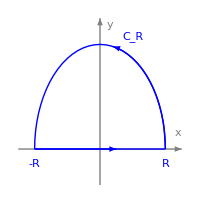
A=∫_-R^R f(z)ⅇ^(ⅈ m z)ⅆz，f(z)=z/(z^2+a^2)满足Jordan引理的条件
故：∫_C_R f(z)ⅇ^(ⅈ m z)ⅆz=0,  被积函数：φ(z)=(z ⅇ^(ⅈ m z))/(z^2+a^2)
∫_-R^R +∫_C_R=2π ⅈ ∑_k Res [φ(z_k)]=2π ⅈ ∑_k Res [f(z_k)ⅇ^(ⅈ m z_k)]
=2π ⅈ (a ⅈ ⅇ^(ⅈ m a ⅈ))/(2a ⅈ)    （z=a ⅈ 为单极点）
A=π ⅈ ⅇ^(-m a)    ⟹    I = π ⅇ^(-m a)  -Graphics-

```mathematica
Clear["Global`*"]

f[x_]:=(x Sin[m x])/(x^2+a^2)
Integrate[f[x],{x,-∞,∞}]
Integrate[f[x],{x,-∞,∞},Assumptions->{m>0,a>0}]
```

ConditionalExpression[(ⅇ^(-Abs[m]/(√(1/a^2))) m π)/Abs[m],m∈Reals&&(Re[a^2]≥0||a^2∉Reals)]

ⅇ^(-a m) π

例题：求积分   （II (b) 型积分）

I=∫_(-∞)^∞ 1/(x^4-1)ⅆx,    （仅为说明方法，其实利用实函数积分即可求解）

解：在实轴上被积函数 f(z)=1/(z^4-1)存在奇点，据广义积分的定义，积分路径应绕过奇点

取积分路径由右图所示，闭合回路内只有一个单极点 z=ⅈ，但实轴上有两单极点 z=±1

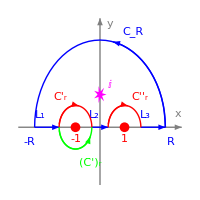
∳_C =∫_L_1 +∫_C'_r +∫_L_2 +∫_C''_r +∫_L_3 +∫_C_R
=2π ⅈ Res f(ⅈ)=2π ⅈ 1/(4 ⅈ^3)=-π/2
 ∫_L_1 =∫_-R^(-1-ε_1),  ∫_L_2 =∫_(-1+ε_1)^(1-ε_2),   ∫_L_3 =∫_(1-ε_2)^R
lim_((R→∞)_((ε_1→0)_(ε_2→0))) [∫_L_1 +∫_L_2 +∫_L_3]=I        -Graphics-

lim_(R→∞) ∫_C_R f(z)ⅆz   ⟹^大圆弧引理  0
lim_(ε_1→∞) ∫_C'_r f(z)ⅆz   ⟹^小圆弧引理  - ⅈ π lim_(z→-1) (z+1)1/(z^4-1)=(ⅈ π)/2
                                                              C'_r 顺时针转 π （见图），故：θ_2-θ_1=-π
lim_(ε_2→∞) ∫_C''_r f(z)ⅆz   ⟹^小圆弧引理  - ⅈ π lim_(z→1) (z-1)1/(z^4-1)=-(ⅈ π)/2
                                                              C''_r 顺时针转 π （见图），故：θ_2-θ_1=-π

综合上述结果  ⟹ I=-π/2。

思考：上述积分路径中仅包围一个奇点 z=ⅈ ，若取绿色小半圆 (C̄')_r 替代 C'_r ，会有不同吗？

例题：求积分  （III (b) 型积分）

I=∫_0^∞ (sin x)/x ⅆx,

解：f(z)=1/z,     z=0点是被积函数 φ(z)=f(z)ⅇ^(ⅈ z)=ⅇ^(ⅈ z)/z 在实轴上的单极点。

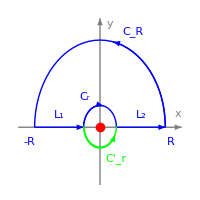
I=1/2 ∫_(-∞)^∞ (sin x)/x ⅆx=1/2 Im [∫_L_1 f(z)ⅇ^(ⅈ z)ⅆz+∫_L_2 f(z)ⅇ^(ⅈ z)ⅆz]
lim_(R→∞) ∫_C_R f(z)ⅇ^(ⅈ z)ⅆz  ⟹^(Jordan 引理) 0
lim_(r→0) ∫_C_r f(z)ⅇ^(ⅈ z)ⅆz  ⟹^小圆弧引理 - ⅈ π lim_(z→0) z φ(z)=-ⅈ π
闭合回路之内无奇点：∫_L_1 +∫_C_r +∫_L_2 +∫_C_R=0
综合上述结果  ⟹ I=1/2 Im[-∫_C_r φ(z)ⅆz]=π/2      -Graphics-

```mathematica
Integrate[Sin[x]/x,{x,0,∞}]
```

π/2

思考：上述积分路径中无奇点，若取绿色小半圆 C'_r 替代 C_r ，会有不同吗？

例题：求积分  （推广型）

I=∫_(-∞)^∞ (sin^2 x)/x^2 ⅆx,

解：如何选取 f(z)?  化为 f(z)ⅇ^(ⅈ m z)型

直接令 f(z)=(sin^2 z)/z^2？  不行， lim_(z→∞) z f(z)≠0, 不宜用大圆弧引理， ∫_C_R f(z)ⅆz≠0

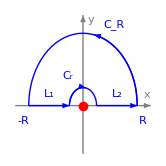
sin z 化为 ⅇ^(ⅈ m z)形式？但分母是二阶零点，可能导致二阶极点
看：sin^2 z=[1/(2ⅈ)(ⅇ^(ⅈ z)-ⅇ^(-ⅈ z))]^2=1/4(1-ⅇ^(2ⅈ z))+1/4(1-ⅇ^(-2 ⅈ z))
4项分别计算？不行，因为被积函数在积分路径上出现二阶极点
取被积函数  φ(z)=1/(2 z^2)(1-ⅇ^(2ⅈ z)) ，   z=0为单极点
在实轴上，Re[φ(z)]=(sin^2 x)/x^2,  且 φ(z) 在实轴上仅有单极点     -Graphics-

设计一个被积函数，除了可用大圆弧引理、Jordan引理外，它还应满足：

a)  实轴上仅有单极点；b) 在实轴其实部或虚部退化为原来的实被积函数

[∫_L_1 +∫_C_r +∫_L_2 +∫_C_R]φ(z)ⅆz=0,   其中：φ(z)=1/(2 z^2)(1-ⅇ^(2ⅈ z)),  Re[φ(z)]=(sin^2 x)/x^2

[∫_L_1 +∫_L_2]φ(z)ⅆz=-[∫_C_r +∫_C_R]φ(z)ⅆz

Re 左=Re[∫_L_1 φ(z)ⅆz+∫_L_2 φ(z)ⅆz]=I，     φ(z)=1/(2 z^2)(1-ⅇ^(2ⅈ z))

∫_C_r φ(z)ⅆz  ⟹^小圆弧引理  -ⅈ π lim_(z→0) z φ(z)=-ⅈ π(-ⅈ),

其中： k=lim_(z→0) z φ(z)= lim_(z→0) (1-ⅇ^(2ⅈ z))/(2z)= lim_(z→0) ((1-ⅇ^(2ⅈ z))')/((2z)')=- lim_(z→0) (2ⅈ ⅇ^(2ⅈ z))/2

∫_C_R φ(z)ⅆz  (⟹_(大圆弧引理 + Jordan 引理))^(φ(z)有 两项，分别利用) 0

综上    ⟹    I=π

例题：求积分  （推广型）

I=∫_(-∞)^∞ (sin^3 x)/x^3 ⅆx,    如何选取 f(z)？化为 f(z)ⅇ^(ⅈ m z)型

(sin^3 x)/x^3=(1/x^3[1/(2ⅈ)(ⅇ^(ⅈ z)-ⅇ^(-ⅈ z))])^3=ⅈ/(8 x^3)((ⅇ^(3ⅈ x)-3 ⅇ^(ⅈ x)+2)_(⏟_二阶零点)+3 ⅇ^(-ⅈ x)-ⅇ^(-3ⅈ x)-2)

上式前三项在 z=0为单极点，

取被积函数：φ(z)=ⅈ/(4 x^3)(ⅇ^(3ⅈ x)-3 ⅇ^(ⅈ x)+2)

在实轴上，Re[φ(z)]=1/x^3 sin^3 x，且 φ(z) 在实轴上仅有单极点

```mathematica
I/(4 x^3)(Exp[3I x]-3Exp[I x]+2);
FullSimplify[ComplexExpand[Re[%]]]
```

Sin[x]^3/x^3

类似前题，可求得：I=(3π)/4

```mathematica
Clear["Global`*"]
f1[x_]:=Sin[x]^2/x^2;
f2[x_]:=Sin[x]^3/x^3;
Integrate[f1[x],{x,-∞,∞}]
Integrate[f2[x],{x,-∞,∞}]
```

π

(3 π)/4

例题：求积分  （推广型）

I=∫_(-∞)^∞ (sin^n x)/x^n ⅆx,   n 为正整数

解：前面对 n=1,2,3情况求解，对一般正整数 n，仿照 n=3的做法很繁。

因为这样做需要把分子分成两项，凑一项为 (n-1)阶零点，以保证被积函数是单极点。

即，应从  sin^n x=[1/(2ⅈ)(ⅇ^(ⅈ z)-ⅇ^(-ⅈ z))]^n 中凑出一项，使得：

a) 该项在 z = 0 为 (n - 1) 阶零点
b) 该项的实部或虚部在实轴等于常数乘以sin^n x }  易乎哉，不易也！

让我们先用 \[MathematicaIcon] Mathematica 试试看能否积出

```mathematica
Clear["Global`*"]
f[x_]:=Sin[x]^n/x^n;
Integrate[f[x],{x,-∞,∞},Assumptions:>{n∈Integers,n>0}]
```

Integrate[x^-n Sin[x]^n,{x,-∞,∞},Assumptions:>{n∈Integers,n>0}]

纳尼？\[MathematicaIcon] Mathematica 也做不出来。

试一试任意给定的正整数 n。发现对任意给定的正整数 n，\[MathematicaIcon] Mathematica 其实可以做出来。只是对一般的 n，无法给出具体表达式。

```mathematica
f[x_]:=Sin[x]^n/x^n;
n=19;
Integrate[f[x],{x,-∞,∞},Assumptions:>{n∈Integers,n>0}]
```

(5278968781483042969 π)/16783438527143608320

对具体的整数，\[MathematicaIcon] Mathematica 还是做出来了，尽管结果复杂了点。

原来， \[MathematicaIcon] Mathematica 应该是有所隐瞒：当结果不是一个简单的表达式时，\[MathematicaIcon] Mathematica 似乎不给力。

现在我们来把它做出来。黔驴技穷，只能设：f(z)=(sin^n z)/z^n，

其实这个函数除了 z=0 是可去奇点之外在全平面都是解析的。

也算风姿绰约，“卿本佳人，奈何为贼？”，撩拨着老衲的心弦。

利用：sin z=(ⅇ^(ⅈ z)-ⅇ^(-ⅈ z))/(2ⅈ)      ⟹^二项式定理    (sin^n z)/z^n=1/(2ⅈ)^n 1/z^n(∑_(k=0))^n(n
k)(-1)^(n-k)ⅇ^(ⅈ (2k-n)z)

被积函数是有限项，可以逐项积分。关注：ⅇ^(ⅈ (2k-n)z)/z^n。选积分回路 C=L+C_R 如图蓝色路径

∳_C (sin^n z)/z^n ⅆz=∫_-R^(+R) (sin^n x)/x^n ⅆx+1/(2ⅈ)^n(∑_(k=0))^n(n
k)(-1)^(n-k)∫_C_R ⅇ^(ⅈ (2k-n)z)/z^n ⅆz
  上式左边为 0，
                    因为卿本佳人，围道内没有奇点（只有可去奇点）
  右边第一项 R→∞ 即为所求 I^，第二项是一些求和
  当  2k-n>0 时，由约当引理，上式第二项  ∫_C_R =0
  当  2k-n=0 且 n>1时，由大圆弧引理，上式第二项  ∫_C_R =0
  当  2k-n<0 时， 约当引理提示  ∫_C'_R =0 而我们需要求 ∫_C_R    -Graphics-

但 ：∫_C'_R + ∫_C_R 构成闭合回路，积分为 2π ⅈ × 全平面留数和！

(故：2k-n<0 时，∫_C_R ⅇ^(ⅈ (2k-n)z)/z^n ⅆz=2π ⅈ × 全平面留数和
   只有一 n 阶极点，故 ∫_C_R=2π ⅈ  Res[ⅇ^(ⅈ (2k-n)z)/z^n]|)_(z=0)=(2π ⅈ)/((n-1)!)ⅈ^(n-1) (2k-n)^(n-1)

——  这里 n 阶极点留数怎么求？（直接展开）

所以：原积分 I=lim_(R→∞) ∫_-R^(+R) (sin^n x)/x^n ⅆx=-1/(2ⅈ)^n(∑_(k=0))^⌊n/2⌋(n
k)(-1)^(n-k)(2π ⅈ)/((n-1)!)ⅈ^(n-1) (2k-n)^(n-1)

整理：I=π/((n-1)!)(∑_(k=0))^⌊ n/2⌋(-1)^k(n
k)(n/2-k)^(n-1)    不是一个简单的表达式，怪不得 \[MathematicaIcon] Mathematica 不假以辞色。

```mathematica
Clear["Global`*"]
f[x_]:=Sin[x]^n/x^n;
n=23;
t1=Integrate[f[x],{x,-∞,∞}]
t2=π/((n-1)!)Sum[(-1)^k Binomial[n,k](n/2-k)^(n-1),{k,0,Floor[n/2]}]
```

(168702835448329388944396777 π)/589300093565066375331840000

(168702835448329388944396777 π)/589300093565066375331840000

思考：求积分：I=∫_(-∞)^∞ (sin^n x)/x^n cos(m x)ⅆx ,    提示： f(z)=(ⅇ^(ⅈ m z)sin^n z)/z^n，I=π/((n-1)!)(∑_(k=0))^⌊ (n-m)/2⌋(-1)^k(n
k)((n-m)/2-k)^(n-1)

##### 吴崇试修订版 p98

解：这里 n 为正整数，m 为整数，不妨设 m>0

J=∳_C (sin^n z)/z^n ⅇ^(ⅈ m z)ⅆz=0  （回路无奇点）
=(∫_-R^(+R) (sin^n x)/x^n ⅇ^(ⅈ m x)ⅆx)_(⏟_(取实部即为所求的 I))+(∫_C_R ((sin^n z) ⅇ^(ⅈ m z))/z^n ⅆz)_(⏟_J')
J'=∫_C_R ((sin^n z) ⅇ^(ⅈ m z))/z^n ⅆz         利用 Euler 公式        -Graphics-

J'=1/(2ⅈ)^n(∑_(k=0))^n(n
k)(-1)^(n-k)∫_C_R (ⅇ^(ⅈ (2k-n)z)ⅇ^(ⅈ m z))/z^n ⅆz            由 Jordan引理，仅在 2k-n+m≤0 时积分非 0
由大圆弧引理，若 2k-n+m=0，仅在 n=1 时有值

n>1 时

J'=1/(2ⅈ)^n(∑_(k=0))^⌊(n-m-1)/2⌋(n
k)(-1)^(n-k)∫_(C_R+C'_R) ⅇ^(ⅈ (2k+m-n)z)/z^nⅆz 
 =(2π ⅈ)/(2ⅈ)^n(∑_(k=0))^⌊(n-m-1)/2⌋(n
k)(-1)^(n-k)Res[ⅇ^(ⅈ (2k+m-n)z)/z^n]_(z=0)
=-π/((n-1)！)(∑_(k=0))^⌊(n-m-1)/2⌋(n
k)(-1)^k((n-m)/2-k)^(n-1)=-π/((n-1)！)(∑_(k=0))^⌊(n-m)/2⌋(n
k)(-1)^k((n-m)/2-k)^(n-1)

n=1 时，因为由 Jordan引理，仅在 2k-n+m≤0 时积分非 0，k≤(n-m)/2≤(1-m)/2

注意到求和指标 k 从 0 开始，故 m=1 才有非 0 值

即 m=n=1，k=0    从而

(J'=-1/(2ⅈ)∫_C_R 1/z ⅆz =-1/(2ⅈ)ln z|)_C_R=-1/(2ⅈ)ⅈ (θ_2-θ_1)=-π/2            C_R 逆时针转 π，故：θ_2-θ_1=π

记得 I=- Re J'

#### \[MathematicaIcon] Mathematica 检验检验

```mathematica
Clear["Global`*"]
f[x_]:=Sin[x]^n/x^n Cos[m x];
n=18;
m=7;
t1=Integrate[f[x],{x,-∞,∞}]
t2=π/((n-1)!)Sum[(-1)^k Binomial[n,k]((n-m)/2-k)^(n-1),{k,0,Floor[(n-m)/2]}]
```

(1225653383267747 π)/237860523343872000

(1225653383267747 π)/237860523343872000

例题：求积分  （推广型）

I=∫_(-∞)^∞ ⅇ^(α x)/(ⅇ^x+1)ⅆx,    0<α<1,      如何选取闭回路

先用 \[MathematicaIcon] Mathematica 牛刀小试           Esc :>Esc    输入  :>

```mathematica
Clear["Global`*"]
f[x_]:=Exp[a x]/(Exp[x]+1);
Integrate[f[x],{x,-∞,∞},Assumptions:>{0<a<1}]    
Integrate[f[x],{x,-∞,∞},Assumptions->{0<a<1}]
```

π Csc[a π]

π Csc[a π]

显然，不是 f(z)ⅇ^(ⅈ m z)型，不宜用Jordan引理，那么能否用大圆弧引理 ？

大圆弧引理需要  lim_(z→∞) z f(z) 在上半平面一致趋于 K，

但显然：g(z)=z f(z)=(z ⅇ^(α z))/(ⅇ^z+1)  在 z 沿虚轴趋于无穷时并不趋于 0 （非孤立奇点）。

0

ComplexInfinity

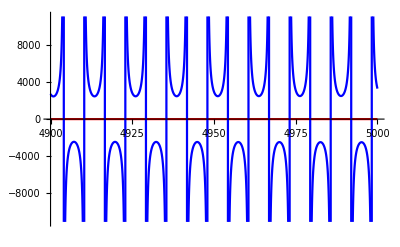

```mathematica
Clear["Global`*"]
g[z_]:=(z Exp[a z])/(Exp[z]+1);
num={a->1/2};

(* 特别注意对自变量趋于无穷，\[MathematicaIcon] Mathematica 的结果似乎不可靠 *)
Limit[g[z]/.num,z-> ∞,Direction->ⅈ]

(* 令 z=1/ζ，换成自变量趋于有限值的极限，并指定极限方向 *)
Limit[g[1/ζ]/.num,ζ->0,Direction->-ⅈ]

Plot[{Re[g[ⅈ y]/.num],Im[g[ⅈ y]/.num]},{y,4900,5000},PlotStyle->{Red,Blue}]
```

如何设计积分回路？f(z)=ⅇ^(α z)/(ⅇ^z+1)，含 ⅇ^z 者可试试矩形回路

“人生到处知何似，往日崎岖还记否”  ，算∫_0^∞ ⅇ^(- a x^2)cos b x ⅆx  时用过这种路径

这种路径的好处是：两竖直边积分可能为 0，积分路径“飘逸离凡尘”

选用右图所示回路（h 值待定）
I=lim_(R→∞) ∫_-R^R ⅇ^(α x)/(ⅇ^x+1)ⅆx=lim_(R→∞) ∫_L_1 f(z)ⅆz
在竖直边 L_2：z=R+ⅈ y,  ⅆz=ⅈ ⅆy
∫_L_2 f(z)ⅆz=∫_0^h (ⅇ^(α (R+ⅈ y))ⅈ ⅆy)/(ⅇ^(R+ ⅈ y)+1)=ⅇ^(-(1-α)R)∫_0^h (ⅇ^(α ⅈ y)ⅈ ⅆy)/(ⅇ^(ⅈ y)+ⅇ^-R)
                                                      α<1, 故：lim_(R→∞) ∫_L_2 f(z)ⅆz=0           -Graphics-

在另一竖直边 L_4：z=-R+ⅈ y,  ⅆz=ⅈ ⅆy

∫_L_4 f(z)ⅆz=∫_0^h (ⅇ^(α (-R+ⅈ y))ⅈ ⅆy)/(ⅇ^(-R+ ⅈ y)+1)=ⅇ^(-α R)∫_0^h (ⅇ^(α ⅈ y)ⅈ ⅆy)/(ⅇ^(-R+ⅈ y)+1)

α>0, 故：lim_(R→∞) ∫_L_4 f(z)ⅆz=0

L_3：z=x+ⅈ h,        故    ∫_L_3 f(z)ⅆz=∫_R^-R (ⅇ^(α (x+ⅈ h)) ⅆx)/(ⅇ^(x+ ⅈ h)+1)=-ⅇ^(ⅈ α h)∫_-R^R (ⅇ^(α x) ⅆx)/(ⅇ^(x+ ⅈ h)+1)

比较 I 的表达式 ：    I=lim_(R→∞) ∫_-R^R ⅇ^(α x)/(ⅇ^x+1)ⅆx，   可知取 h=2π，

则：lim_(R→∞) ∫_L_3 f(z)ⅆz=-ⅇ^(ⅈ α 2π)I

故：lim_(R→∞) [∫_L_1 +∫_L_2 +∫_L_3 +∫_L_4]=(1-ⅇ^(ⅈ α 2π))I

但由留数定理：∫_L_1 +∫_L_2 +∫_L_3 +∫_L_4=∳=2π ⅈ Res f(π ⅈ)=2π ⅈ ⅇ^((α-1)ⅈ π)

综上所求：I=π/(sin α π)

例题：求积分  （推广型）

I=∫_(-∞)^∞ (sin x)/(sh x)ⅆx

解：先用 \[MathematicaIcon] Mathematica 牛刀小试，被积函数的原函数是特殊函数

```mathematica
Clear["Global`*"]
f[x_]:=Sin[ x]/Sinh[x];
t=Integrate[f[x],x]
Limit[t,x->∞]-Limit[t,x->-∞]
FullSimplify[%]
Integrate[f[x],{x,-∞,∞}]
```

(1/2+ⅈ/2) ⅇ^((1-ⅈ) x) (-ⅈ Hypergeometric2F1[1/2-ⅈ/2,1,3/2-ⅈ/2,ⅇ^(2 x)]+ⅇ^(2 ⅈ x) Hypergeometric2F1[1/2+ⅈ/2,1,3/2+ⅈ/2,ⅇ^(2 x)])

(1/2-ⅈ/2) ⅇ^(-π/2) (-ⅈ Gamma[1/2+ⅈ/2] Gamma[3/2-ⅈ/2]+ⅇ^π Gamma[1/2-ⅈ/2] Gamma[3/2+ⅈ/2])

π Tanh[π/2]

π Tanh[π/2]

类似上题，取被积函数 ：φ(z)=f(z)ⅇ^(ⅈ z), f(z)=1/(sh z)

当 z 沿虚轴趋于无穷时 f(z)并不为 0。

```mathematica
Clear["Global`*"]
f[z_]:=1/Sinh[z];
Limit[f[1/ζ],ζ->0,Direction->-ⅈ]
```

ⅈ Interval[{-∞,-1},{1,∞}]

尝试取积分回路为：
正实轴，经第一象限的 1/4 圆周，再由正虚轴返回原点，
这时虽有 ∫_C_R=0，但困难在于
虚轴上有无穷多个奇点：z_k=ⅈ  k π, k=0,1,2,...
在虚轴：∫φ(z)ⅆz=∫_R^ε ⅇ^-y/(sin y)ⅆy  经过无穷多单极点，不易求     -Graphics-

取积分回路如图。（记得含 ⅇ^z 者可试试矩形回路）被积函数 φ(z)=ⅇ^(ⅈ z)/(sh z)在回路之内无奇点

I=∫_(-∞)^∞ (sin x)/(sh x)ⅆx=Im∫_-R^R φ(z)ⅆz=Im J,    J=∫_-R^R ⅇ^(ⅈ z)/(sh z)ⅆz,  φ(z)=f(z)ⅇ^(ⅈ z), f(z)=1/(sh z)

∫_L_1 +∫_C'_r +∫_L_2 +∫_L_3 +∫_L_4 +∫_C''_r +∫_L_5 +∫_L_6=0
R→∞ 且 r→0时，Im[∫_L_1 φ(z)ⅆz+∫_L_2 φ(z)ⅆz]=J
L_3：z=R+ⅈ y ,
 ∫_L_3 φ(z)ⅆz=∫_0^π (2 ⅇ^(ⅈ (R+ⅈ y)))/(ⅇ^(R+ⅈ y)-ⅇ^(-R-ⅈ y))ⅆ(ⅈ y)
=2ⅈ ⅇ^(ⅈ R-R)∫_0^π ⅇ^-y/(ⅇ^(ⅈ y)-ⅇ^(-2R-ⅈ y))ⅆy=0
类似地，∫_L_6 φ(z)ⅆz=0     -Graphics-

[∫_L_4 +∫_L_5]φ(z)ⅆz=[∫_L_4 +∫_L_5]ⅇ^(ⅈ x - π)/(-sh x)ⅆx=ⅇ^-π J ,         记得：φ(z)=f(z)ⅇ^(ⅈ z), f(z)=1/(sh z)

∫_C'_r φ(z)ⅆz  ⟹^小圆弧引理  -ⅈ π  lim_(z→0) z φ(z)=-ⅈ π      （顺时针转 π，故：ⅈ(θ_2-θ_1)=-ⅈ π）

∫_C''_r φ(z)ⅆz  ⟹^小圆弧引理  -ⅈ π lim_(z→ⅈ π) (z-ⅈ π) φ(z)=-ⅈ π ⅇ^-π/(ch ⅈ π)=ⅈ π ⅇ^-π

综上，(1.EquationNumbered)式两边取虚部并利用 I=Im J 得：(1+ⅇ^-π)I-π(1-ⅇ^-π)=0

即： I=π tanh π/2

例题：求积分  （推广型）

I=∫_0^∞ x/(ⅇ^x-1)ⅆx

含有 ⅇ^x 型的积分，常用矩形回路，含有三角函数的，常用大圆弧。

解：先用 \[MathematicaIcon] Mathematica 牛刀小试，注意 PolyLog 是一个特殊函数。Li_n(z)=(∑_(k=1))^∞z^k/k^n

```mathematica
Clear["Global`*"]
f[x_]:=x/(ⅇ^x-1);
g=Integrate[f[x],x]
(* g 中的任意一项，在 x -> ∞ 时极限都为无穷大，但三项之和极限存在 *)
Limit[g,x->∞];
Limit[g,x->∞]-Limit[g,x->0] 
Integrate[f[z],{z,0,∞}]
```

-x^2/2+x Log[1-ⅇ^x]+PolyLog[2,ⅇ^x]

π^2/6

π^2/6

定义被积函数：f(z)=z/(ⅇ^z-1)，取右图所示积分路径
若矩形高度 h =2π 
            可保证 L_1 与 L_3 两段被积函数的分母相同
当 R→∞ 且 r→0时，在 L_3：z=x+ⅈ h
∫_L_1 f(z)ⅆz=I,     ∫_L_3 f(z)ⅆz=-I-2π ⅈ∫_0^∞ ⅆx/(ⅇ^x-1),  
在 L_1 与 L_3 两段，I 相消，求不出 I。      -Graphics-

故矩形高度取为 h= π，不必绕开 ⅈ h 点，积分回路如右下图
当 R→∞ 且 r→0时，
仍有：∫_L_1 f(z)ⅆz=I,   在 L_3: z=x+ⅈ π,  ⅆz=ⅆx
∫_L_3 f(z)ⅆz=∫_0^∞ (x+ⅈ π)/(e^x+1)ⅆx=∫_0^∞ xⅆx/(ⅇ^x+1)+ⅈ π∫_0^∞ ⅆx/(ⅇ^x+1)
                      积分 ∫_L_3 f(z)ⅆz 似乎与 I 无关？实部可化为 I
∫_C_r f(z)ⅆz→^小圆弧引理 ⅈ (- π/2)lim_(z→0) z f(z)=0  -Graphics-

L_2：z=R+ⅈ y,    ∫_L_2 f(z)ⅆz=∫_0^h (R+ⅈ y)/(ⅇ^(R+ⅈ y)-1)ⅆ(ⅈ y)=ⅈ R ⅇ^-R∫_0^h ((1+ⅈ y/R)ⅆy)/(ⅇ^(ⅈ y)-ⅇ^-R)=0

I_4≡∫_L_4 f(z)ⅆz=- ∫_0^h (ⅈ y)/(ⅇ^(ⅈ y)-1)ⅆ(ⅈ y)           利用了在 L_4：z=ⅈ y
=∫_0^h (y (ⅇ^(-ⅈ y)-1))/(2-2cos y)ⅆy=∫_0^h (y (cos y-1+ⅈ sin y))/(2-2cos y)ⅆy    目的是分出虚、实部
=-1/2∫_0^h yⅆy-ⅈ∫_0^h (y sin y)/(2-2cos y)ⅆy

回路内无奇点：∫_L_1 +∫_L_2 +∫_L_3 +∫_L_4 +∫_C_r=0,   （蓝色项为 0）

(1.EquationNumbered)式取实部，有：

∫_0^∞ x/(e^x-1)ⅆx+∫_0^∞ x/(e^x+1)ⅆx-1/2∫_0^π yⅆy=0，

蓝色部分：∫_0^∞ x/(e^x+1)ⅆx  如何与 I =∫_0^∞ x/(e^x-1)ⅆx 关联？

利用：x/(ⅇ^x-1)-x/(ⅇ^x+1)=(2x)/(ⅇ^(2x)-1)  两边同时积分

∫_0^∞ xⅆx/(ⅇ^x-1)-∫_0^∞ xⅆx/(ⅇ^x+1)=∫_0^∞ (2xⅆx)/(ⅇ^(2x)-1) ⟹^(令：y = 2x)  1/2∫_0^∞ yⅆy/(ⅇ^y-1)

从而：∫_0^∞ xⅆx/(ⅇ^x+1)=1/2∫_0^∞ xⅆx/(ⅇ^x-1)=1/2 I,  代入 (1.EquationNumbered)得

I=∫_0^∞ xⅆx/(ⅇ^x-1)=π^2/6

至于(1.EquationNumbered)式的虚部，“顺手牵羊”给出： π∫_0^∞ ⅆx/(ⅇ^x+1)=∫_0^π (y sin y)/(2-2cos y)ⅆy

```mathematica
Integrate[π/(ⅇ^x+1),{x,0,∞}]
Integrate[(y Sin[y])/(2(1-Cos[y])),{y,0,π}]
```

π Log[2]

π Log[2]

另解：I=∫_0^∞ x/(ⅇ^x-1)ⅆx,   取 f(z)=z^2/(ⅇ^z-1)    不同于 z/(ⅇ^z-1)           三十六计之“假道伐虢、借尸还魂”

积分路径如上图，h=2π, 当 r→0, R→∞ 时，
∫_L_1 f(z)ⅆz=∫_0^∞ x^2/(ⅇ^x-1)ⅆx≠I
∫_L_3 f(z)ⅆz=-∫_0^∞ (x+2ⅈ π)^2/(ⅇ^x-1)ⅆx
∫_L_1 +∫_L_3=-4ⅈ π I +4 π^2(∫_0^∞ ⅆx/(ⅇ^x-1))_(⏟_这个积分发散)
∫_C'_r f(z)ⅆz=-ⅈ π/2 lim_(z→0) z f(z)=0
∫_C''_r f(z)ⅆz=-ⅈ π/2 lim_(z→2π ⅈ) (z-2π ⅈ) f(z)=2ⅈ  π^3   -Graphics-

L_2：z=R+ⅈ y,    ∫_L_2 f(z)ⅆz=∫_0^h (R+ⅈ y)^2/(ⅇ^(R+ⅈ y)-1)ⅆ(ⅈ y)=ⅈ R^2 ⅇ^-R∫_0^h ((1+ⅈ y/R)^2 ⅆy)/(ⅇ^(ⅈ y)-ⅇ^-R)=0

∫_L_4 f(z)ⅆz=ⅈ∫_0^(2π) (y^2 ⅆy)/(ⅇ^(ⅈ y)-1)=-ⅈ/2∫_0^(2π) y^2 ⅆy+1/2∫_0^(2π) (y^2 sin y)/(1-cos y)ⅆy

∫_L_1 +∫_L_3 +∫_L_2 +∫_C'_r +∫_C''_r +∫_L_4=2π ⅈ ∑_k Res f(z_k)=0，

上式两边同取虚部：-4π I+2 π^3-1/2∫_0^(2π) y^2 ⅆy=0      ⟹     I=π^2/6

若两边同取实部，则得：1/2∫_0^(2π) (y^2 sin y)/(1-cos y)ⅆy=4 π^2∫_0^∞ ⅆx/(ⅇ^x-1)，很不幸，两项均为发散。

```mathematica
Integrate[1/(Exp[x]-1),{x,0,∞}]
Integrate[y y Sin[y]/(1-Cos[y]),{y,0,2π}]
```

Integrate::idiv: Integral of 1/-1 + ⅇ^x does not converge on {0, ∞}.

∫_0^∞ 1/(-1+ⅇ^x)ⅆx

Integrate::idiv: Integral of y^2\ Cot[y/2] does not converge on {0, 2\ π}.

∫_0^(2 π) (y^2 Sin[y])/(1-Cos[y])ⅆy

例题：求 Fresnel 积分  （推广型）

I=∫_0^∞ cos x^2 ⅆx

解：取 f(z)=ⅇ^(ⅈ z^p), 积分回路包含大圆弧，应用大圆弧引理

大圆弧作到什么角度？    lim_(z→∞) z f(z)  有界的方位

lim_(z→∞) z f(z)=lim_(z→∞) z ⅇ^(ⅈ z^2)
=lim_(R→∞) R ⅇ^(ⅈ θ)ⅇ^(ⅈ R^2 cos 2θ-R^2 sin 2θ)
 仅当  sin 2θ>0 时，
才满足大圆弧引理条件：lim_(z→∞) z f(z)=存在   -Graphics-

⟹  在 0<θ<π/2 有   ∫_C_R f(z)ⅆz=0

设大圆弧为 1/4 圆弧，回路为：正实轴 L_1，1/4 圆弧 C_R，正虚轴 L_2

∫_L_1 f(z)ⅆz=∫_0^∞ ⅇ^(ⅈ x^2)ⅆx         —— 实部为所求 I

∫_L_2 f(z)ⅆz=-∫_0^∞ ⅇ^(-ⅈ y^2)ⅆ(ⅈ y)=-ⅈ∫_0^∞ ⅇ^(-ⅈ y^2)ⅆy

∫_L_1 +∫_L_2 +∫_C_R=0   →^(两边分别取虚、实部) ∫_0^∞ cos x^2 ⅆx=∫_0^∞ sin x^2 ⅆx

设大圆弧为 1/8 圆弧，回路为：正实轴 L_1，1/8 圆弧 C_R， L_2：z=r ⅇ^(ⅈ π/4)

仍有：∫_L_1 f(z)ⅆz=∫_0^∞ ⅇ^(ⅈ x^2)ⅆx,     L_2:  z=r ⅇ^(ⅈ π/4),      z^2=ⅈ r^2

∫_L_2 f(z)ⅆz=-∫_0^∞ ⅇ^(ⅈ (ⅈ r^2))ⅇ^(ⅈ π/4)ⅆr=-ⅇ^(ⅈ π/4)∫_0^∞ ⅇ^(-r^2)ⅆr=-ⅇ^(ⅈ π/4)(√π)/2

∫_L_1 +∫_L_2 +∫_C_R=0

→^(分别取虚、实部) ∫_0^∞ cos x^2 ⅆx=∫_0^∞ sin x^2 ⅆx =(√(2π))/4

```mathematica
Clear["Global`*"]
f[z_]:=Cos[z^2];
Integrate[f[x],x]
Integrate[f[z],{z,0,∞}]
```

√(π/2) FresnelC[√(2/π) x]

(√(π/2))/2

思考：求积分：I_1=∫_0^∞ cos x^p ⅆx ,  I_2=∫_0^∞ sin x^p ⅆx      (p>1)    超越普利瓦洛夫留数卷 p89

答案：I_1=1/p Γ(1/p)cos π/(2p)， I_2=1/p Γ(1/p)sin π/(2p)

解：取 f(z)=ⅇ^(ⅈ z^p), 积分回路包含大圆弧，应用大圆弧引理

大圆弧作到什么角度？    lim_(z→∞) z f(z)  有界的方位

lim_(z→∞) z f(z)=lim_(z→∞) z ⅇ^(ⅈ z^p)
=lim_(R→∞) R ⅇ^(ⅈ θ)ⅇ^(ⅈ R^p cos p θ-R^p sin p θ)
 仅当  sin p θ>0 时，
才满足大圆弧引理条件：lim_(z→∞) z f(z)=存在   -Graphics-

0<θ<π/p 时，有   ∫_C_R f(z)ⅆz=0

设大圆弧为 π/(2p)圆弧，

回路为：正实轴 L_1，π/(2p)圆弧 C_R， L_2：z=r ⅇ^(ⅈ π/2p)，C_r  小圆弧

为何要做小圆弧：因为 z=0 是枝点，枝点是奇点，奇点如官员出行：“威武”，“回避”

前知： ∫_C_R f(z)ⅆz=0，  ∫_C_r f(z)ⅆz  ⟹^小圆弧引理  lim_(r→0) ∫_C_r f(z)ⅆz=0

仍有：∫_L_1 f(z)ⅆz=∫_0^∞ ⅇ^(ⅈ x^p)ⅆx,     L_2:  z=r ⅇ^(ⅈ π/2p),     z^p=ⅈ r^p

∫_L_2 f(z)ⅆz=-∫_0^∞ ⅇ^(ⅈ (ⅈ r^p))ⅇ^(ⅈ π/2p)ⅆr=-ⅇ^(ⅈ π/2p)∫_0^∞ ⅇ^(-r^p)ⅆr=-1/pΓ(1/p)ⅇ^(ⅈ π/2p)

∫_0^∞ ⅇ^(-r^p) ⅆr   (⟹_(ⅆr = ⅆx/p x^((p-1)/p)))^(令 r^p= x) 1/p(∫_0^∞ x^(1/p-1)ⅇ^-x ⅆx)_(⏟_(Γ(1/p)))=1/p Γ(1/p)

∫_L_1 +∫_L_2 +∫_C_R +∫_C_r=0

→^(分别取虚、实部){∫_0^∞ cos x^p ⅆx=1/p Γ(1/p)cos π/(2p)
∫_0^∞ sin x^p ⅆx=1/p Γ(1/p)sin π/(2p)

## 4.3 应用留数定理计算级数和

根据留数定理，对不容易计算的积分，可以通过求留数和来求积分

留数和 ⟹ 积分值    即： ∳_C f(z)ⅆz = 2π ⅈ∑_k Res f(z_k)

反过来，若积分本身容易计算，那就可以通过求积分值来求得留数和。

积分值 ⟹ 留数和   即： ∑_k Res f(z_k)=1/(2π ⅈ)∳_C f(z)ⅆz

什么情况下需要求留数和？当被积函数的每一个留数都对应于某个级数的每一项，

那么，求得留数和就是求得了级数和。因而可以通过复变函数的积分来求级数和。

∑_k a_k=∑_k Res f(z_k)=1/(2π ⅈ)∳_C f(z)ⅆz

为了此目的，需要做以下两步：

设计恰当的复变函数，使得该函数的每一个留数对应于一个级数的每一项；

寻找一个能简单计算该复变函数积分的方法，最好形如大圆弧引理那样简单。

以下定理解决了这两步。

定理：设函数 f(z) 在整个复平面处有限个孤立奇点外处处解析，若存在常数 M>0 和 R>0 ，使得

当  |z|>R 时，|z f(z)|<M，（即在无穷远领域，|z f(z)| 有界）则：

lim_(N→∞) ∳_C_N f(z)ctg πz ⅆz=0，

lim_(N→∞) ∳_C_N f(z)csc πz ⅆz=0，

lim_(N→∞) ∳_L_N f(z)tg πz ⅆz=0，

lim_(N→∞) ∳_L_N f(z)sec πz ⅆz=0

其中 C_N 为顶点于 (N+1/2)(1±ⅈ), -(N+1/2)(1±ⅈ) 的正方形，如图所示。

L_N 为顶点于 N(1±ⅈ), -N(1±ⅈ) 的正方形，N 为正整数

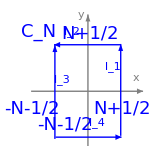
-Graphics-           -Graphics-

证明：该定理的证明较为复杂

以 (1.EquationNumbered) 为例：  I=∳_C_N f(z)ctg πz ⅆz ，需证 I=0

证明为 0 常取绝对值： |I|≤ ∳_C_N |z f(z) |  |ctg π z| |ⅆz/z|， （因为|z f(z)|有界，故凑成蓝色部分）

考虑以下四点。

1.   |ctg π z| 在 C_N 上是否有界：|ctg π z|≤M'？                       ☺

2.  因 N→∞ 时，∳_C_N |ⅆz/z|有界，那么是否有：|z f(z)|→0？   ☹

3.  条件：|z f(z)|<M,    能否化为：|z f(z)-κ|→0？          ☺   （记得好像讲过有界必有极限？条件？）

4.  I 能否写成： I≡∳_C_N f(z)ctg πz ⅆz  = ∳_C_N [z f(z)-κ]ctg πz ⅆz/z                        ☺

1.    先证明在 C_N 上   |ctg π z| ≤M'  有界

利用  |ctg (z+N π)|=|ctg z| 及 |ctg (z+1/2 π)|=|tg z|

在 l_1：z=(N+1/2)+ⅈ y,

|ctg π z|=| tg (ⅈ π y) |=|(ⅇ^(π y)-ⅇ^(-π y))/(ⅇ^(π y)+ⅇ^(-π y))|≤1

在 l_3：z=-(N+1/2)+ⅈ y,

|ctg π z|=| tg (ⅈ π y) |=|(ⅇ^(π y)-ⅇ^(-π y))/(ⅇ^(π y)+ⅇ^(-π y))|≤1

在 l_2：z=x+(N+1/2)ⅈ=x+(A/π) ⅈ,   A=(N+1/2)π>0

|ctg π z|=|(ⅇ^(ⅈ π z)+ⅇ^(-ⅈ π z))/(ⅇ^(ⅈ π z)-ⅇ^(-ⅈ π z))|=|(ⅇ^(ⅈ π x)ⅇ^-A+ⅇ^(-ⅈ π x)ⅇ^A)/(ⅇ^(ⅈ π x)ⅇ^-A-ⅇ^(-ⅈ π x)ⅇ^A)|
=|(1+ⅇ^(2ⅈ π x)ⅇ^(-2A))/(1-ⅇ^(2ⅈ π x)ⅇ^(-2A))|       在 A=(N+1/2)π →∞ 时 有界

类似地，在 l_4：z=x-(N+1/2)ⅈ=x-(A/π) ⅈ,

|ctg π z|=|(ⅇ^(ⅈ π x)ⅇ^A+ⅇ^(-ⅈ π x)ⅇ^-A)/(ⅇ^(ⅈ π x)ⅇ^A-ⅇ^(-ⅈ π x)ⅇ^-A)|
=|(1+ⅇ^(-2ⅈ π x)ⅇ^(-2A))/(1-ⅇ^(-2ⅈ π x)ⅇ^(-2A))|     有界

2.     显然，定理的条件是  |z f(z)|<M 而非 |z f(z)|→0。

3.   另辟捷径，证明：存在一常数 κ，使得  |z f(z)-κ|→0。

|z|>R 时，|z f(z)|<M，故  h(z)=z f(z) 在 z=∞ 邻域有界，

邻域有界，必为可去奇点（根据可去奇点的充要条件），

即： z=∞ 是 h(z)的可去奇点，作 Laurent 展开无正幂次项

h(z)=a_0+a_1/z+a_2/z^2+...                且在 ∞ 邻域“内闭一致收敛”。

h(z)-a_0 当然也“内闭一致收敛”，s=z [h(z)-a_0] 自然也“内闭一致收敛”。

即：级数  s=(a_1+a_2/z+a_3/z^2...)也在 ∞ 邻域内闭一致收敛，

由Weierstrass定理，级数的和函数 s 解析且可逐项求导，自然也就有界：|s|≤ M''

而  z f(z)-a_0=1/z s    ⟹   J= |z f(z)-a_0|≤ M''/(|z|)，

此式的意义为：当|z|足够大，J 可小于任意小

即：lim_(z→∞) z f(z) =κ   或   z→∞ 时，|z f(z)-κ|→0，其中   κ=a_0

这里实际上是在证明：在孤立奇点邻域有界与存在极限是等价的。

（请回顾孤立奇点类型的判断部分，当时仅仅对有界区域的奇点做了证明）

简而言之，这一步是在证明：

|z f(z)| 有界   (⟹_极限存在)^有界等价于  lim_(z→∞) z f(z)=κ    (⟹_这其实是极限的定义)^(|z | > R 时)  |z f(z)-κ|<ε

4.   最后证明  I≡∳_C_N f(z)ctg πz ⅆz=∳_C_N [z f(z)-κ]ctg πz ⅆz/z

为此，需证：c=∳_C_N (ctg πz)/z ⅆz=0，   令：被积函数：g(z)=(ctg πz)/z

据留数定理：c=2π ⅈ Res g(0)+2π ⅈ (∑_(k=1))^N[Res g(k)+Res g(-k)]

g(z)为偶函数，以 z=0为中心的 Laurent 展开式只有偶幂次，故：Res g(0)=0

在单极点 k，Res g(k)=lim_(z→k) ((cos π z)/z)/((sin π z)')=1/(k π),    Res g(-k)=-1/(k π)

正负 k 的留数相消，故：c=∳_C_N (ctg πz)/z ⅆz=0。

⟹ I=∳_C_N f(z)ctg πz ⅆz=∳_C_N (f(z)-κ/z)ctg πz ⅆz，κ 可以为任意常数

综合以上四点

|I|≡|∳_C_N f(z)ctg πz ⅆz |
=| ∳_C_N [f(z)-a_0/z]ctg πz ⅆz |          记得 κ=a_0
≤ ∳_C_N |z f(z)-a_0| |ctg πz| |ⅆz/z|，因为 ：|z f(z)-a_0|→0
≤ M' ε∳_C_N (|ⅆz|)/(|z|) ， 因为 ：∳_C_N (|ⅆz|)/(|z|)<M'' 有界
≤  M' ε M''

故：lim_(N→∞) I=0,  得证。

(1.EquationNumbered) 式中 ∳_C_N f(z)ctg πz ⅆz 在 z=n 是孤立奇点，因而可用于求 ∑_n f(n) 形式的级数和

当然条件是 z=n 不是 f(n) 的奇点，否则 f(n) 可能就不存在

(1.EquationNumbered) 式中 ∳_C_N f(z)csc πz ⅆz 在 z=n 是孤立奇点，因而可用于求 ∑_n (-1)^n f(n) 形式的级数和

(1.EquationNumbered) 式中∳_L_N f(z)tg πz ⅆz  在 z=(n+1/2) 是孤立奇点，因而可用于求 ∑_n f(n+1/2) 形式的级数和

(1.EquationNumbered) 式中 ∳_L_N f(z)sec πz ⅆz 在 z=(n+1/2) 是孤立奇点，因而可用于求 ∑_n (-1)^n f(n+1/2) 形式的级数和

用这种正方形回路总觉得不方便，利用圆形回路 C_R 如何？ ——  思考？

例题：试求级数和 I=(∑_(n=1))^∞1/n^2                     ——   ∑_n f(n)  型

取 f(z)=1/z^2，由定理知：∳_C_N f(z)ctg π zⅆz=0

令 φ(z)=(ctg π z)/z^2=(cos π z)/(z^2 sin π z),     ⟹       2π ⅈ ∑_n Res φ(z_n) =0

φ(z)的奇点为 z=±n，n=0,1,2,...

z=±n，n≠0 是单极点，Res φ(±n)=lim_(z→±n) (cos π z/z^2)/((sin π z)')=1/π 1/n^2

z=0 是三阶极点，Res φ(0)=lim_(z→0) 1/(2!)(z ctg π z)''=-π/3

```mathematica
Clear["Global`*"]
f[z_]:=z Cot[π z];
D[f[z],{z,2}];
Limit[1/(2!)%,z->0]
Sum[1/n^2,{n,1,∞}]
```

-π/3

π^2/6

从而：∑_n Res φ(z_n)=((∑_(n=1))^∞2/π 1/n^2)-π/3=0  ⟹  (∑_(n=1))^∞1/n^2=π^2/6

例题：试求级数和 I=(∑_(n=-∞))^∞(-1)^n/(2n+1)^3，                  ——   ∑_n (-1)^n f(n+1/2)  型

f(z)=1/z^3,   φ(z)=f(z)sec π z,

由 (1.EquationNumbered)式，∳_L_N φ(z)ⅆz=0=2π ⅈ ∑_k φ(z_k)

φ(z)的奇点为：z= 0 和 z=z_n=n+1/2，n=0,±1,±2,...

z_n 是单极点，n≠0 时

Res φ(z_n)=lim_(z→z_n) (1/z^3)/((cos π z)')=1/(n+1/2)^3(-1/π)1/(sin(n π+π/2))=-(-1)^n/((n+1/2)^3 π)

z=0是三阶极点

Res φ(0)=lim_(z→0) 1/(2！)(sec π z)''=π^2/2

```mathematica
g[z_]:=Sec[π z]
D[g[z],{z,2}];
Limit[%,z->0]
```

π^2

综上，(∑_(n=-∞))^∞(-1)^n/(n+1/2)^3=π^3/2    ⟹   I=(∑_(n=-∞))^∞(-1)^n/(2n+1)^3=π^3/16

```mathematica
Sum[(-1)^n/(2n+1)^3,{n,-∞,∞}]
FullSimplify[%]
```

1/64 (2 π^3+Zeta[3,1/4]-Zeta[3,3/4])

π^3/16

## 4.4 对数留数 辐角原理 Rouche 定理

在本课程一开始，我们曾说引入复数在某种意义上是为了 n 次多项式有 n 个根。

本节基于留数定理给予证明。也介绍一些涉及到的基本概念。（参见  § 2.2  Liouville 定理章节的例题 的另一种证明）

### 对数留数

定义：如下积分称为函数 f(z) 关于闭合曲线 C 的对数留数

I=1/(2π ⅈ)∳_C (f'(z))/(f(z))ⅆz

定理：若 f(z) 在简单闭合曲线 C 上解析并且不为零，在 C 内部除了有限个极点外也解析，则

I=1/(2π ⅈ)∳_C (f'(z))/(f(z))ⅆz=N-P           注：被积函数分母含 f(z)，故要求 C 上 f(z)≠0

其中：{ N=∑_i n_i ， 求和对 C 内的零点进行，n_i 为零点阶数
P=∑_j p_j ， 求和对 C 内的极点进行，p_j 为极点阶数    极点相当于“负零点”

证明：令：g(z)=(f'(z))/(f(z))

由第三章例题知

a)：f(z)的一个 p_j 阶极点，必为 g(z)的单极点，且留数为 -p_j

证：对一个 n_i 阶极点 z_i，有：f(z)=(z-z_i)^-n_i ψ(z)     其中 ϕ(z) 解析且  ϕ(z_i)≠0

故：f'(z)=-(n_i(z-z_i))^(-n_i-1)ψ(z)+(z-z_i)^-n_i ψ'(z)

(f'(z))/(f(z))=-n_i/(z-z_i)+(ψ'(z))/(ψ(z))，因为  ϕ(z_i)≠0，故 z_i 为 g(z)的单极点，且留数为 n_i

另一方面

b)： f(z)的一个 n_i 阶零点，必为 g(z)的单极点，且留数为 n_i

证：对一个 n_i 阶零点 z_i，有：f(z)=(z-z_i)^n_i ϕ(z)     其中 ϕ(z) 解析且  ϕ(z_i)≠0

故：f'(z)=(n_i(z-z_i))^(n_i-1)ϕ(z)+(z-z_i)^n_i ϕ'(z)

(f'(z))/(f(z))=n_i/(z-z_i)+(ϕ'(z))/(ϕ(z))，因为  ϕ(z_i)≠0，故 z_i 为 g(z)的单极点，且留数为 n_i

联立 a) 和 b) ，并应用留数定理，该定理得证。

### 辐角原理 —— 对数留数的几何意义

当 z 沿某简单闭曲线 C 绕行一周时，在 w=f(z) 平面画出的曲线 Γ 不一定是简单曲线。

-Graphics-       -Graphics-

上图显示 z 平面的简单闭曲线 C 经 w=f(z) 映照到在 w 平面 Γ 不一定是简单曲线。

若在简单闭曲线 C 上 f(z)≠0，则  Γ 不经过 w 平面的原点。

那么，问题是： z 平面绕原点一周的曲线 C，映射到 w 平面的 Γ 绕原点的几周？

——  等于解析函数 f(z) 关于闭合曲线 C 的对数留数！

此即：辐角原理

定理：若函数 f(z) 在简单闭合曲线 C 上及 C 内单值解析，并且在 C 上，f(z)≠0，则 f(z) 在 C 内的零点个数

等于1/(2π) 乘以 C 正向绕行一周时，f(z)在对应的 w 平面的辐角改变量，记为：Δ_(C+)arg f(z)。

证明：

1/(2π ⅈ)∳_C (f'(z))/(f(z))ⅆz=1/(2π ⅈ)∳_C ⅆln f(z)=1/(2π ⅈ)∳_Γ ⅆln w

但：ln w=ln|w|+ⅈ arg w

C 正向绕行一周回出发点时，在 w 平面，也沿曲线 Γ 回出发点，因为 f(z)单值解析

ln|w| 不变， arg w 的改变即为 w 平面的辐角改变量。

方程 (1.EquationNumbered)的含义： { 左=1/(2π ⅈ)∳_C (f'(z))/(f(z))ⅆz=N-P ⟹^(C 内解析) N 即 f(z) 零点个数
右=1/(2π)( w 平面内沿曲线 Γ 一周辐角改变量)
=曲线 Γ 绕原点的圈数

简而言之：解析函数 f(z) 在 z 平面简单闭合曲线 C 内有几个根（一个 m 阶零点算 m 个根），

则曲线C 映照到 w 平面上的 Γ 曲线就在w 平面绕原点几圈

如果把零点称为“愁”，赋予“幅角原理”一点诗意：“问君能有几多愁，恰似绕着原点走一走! ”

### Rouche 定理

辐角原理将简单闭合曲线 C 所包围的解析函数 f(z) 的零点数（ 即 f(z) 的根的数目）

与 f(z) 在 w 平面辐角的改变量联系起来，即与 w 平面绕原点圈数联系起来，

从而开创了研究方程根的新方法。Rouche 定理就是一个简单实例。

Rouche 定理：设 f(z) 和 g(z) 在简单闭合曲线 C 上和 C 内区域 D 上解析，并且，在曲线 C 上恒有 |f(z)|>|g(z)|

则 f(z) 在 C 内的零点个数 N 等于 h(z)=f(z)+g(z) 的零点个数 N'。

理解：我们知道，如果在闭区域 D+C 上 |g(z)|<|f(z)|，则 f(z)+g(z) 的零点数与 f(z) 相同；

其实这时 f(z)+g(z) 与 f(z) 的零点也相同

Rouche定理说，要保证 f(z)+g(z) 的零点数就与 f(z) 相同，只需在边界 C 上  |g(z)|<|f(z)|

这时 f(z)+g(z) 与 f(z) 的零点个数相同，零点本身可能不同

证明：  在曲线 C 上： |f(z)|>|g(z)|≥0       ⟹   |f(z)|>0

|f(z)+g(z)|> |f(z)|-|g(z)|>0   ⟹   |f(z)+g(z)|>0

故在 C 上， f(z)≠0,  f(z)+g(z)≠0，注意这一点是辐角原理的条件（解析+ 非零）

设  C 内 f(z) 和 f(z)+g(z) 的零点个数分别为 N 和 N'

由辐角原理：{ N=1/(2π)Δ_(C+)arg f(z)
N'=1/(2π)Δ_(C+)arg [f(z)+g(z)]

arg [f(z)+g(z)]=arg {f(z)[1+(g(z))/(f(z))]}=arg f(z)+arg [1+(g(z))/(f(z))]_(⏟_w)

N'=1/(2π)Δ_(C+)arg [f(z)+g(z)]=(1/(2π)Δ_(C+)arg f(z))_(⏟_N)+(1/(2π)Δ_(C+)arg [1+(g(z))/(f(z))])_(⏟_M)

注意写成乘积形式，辐角才是相加，且  h(z)=f(z)+g(z)   在 C 上不为 0，可应用辐角原理 。

观察 h(z) 绕原点的圈数 N'，而 N'-N=M

M=1/(2π)Δ_(C+)arg [1+(g(z))/(f(z))] 是在 z 平面上沿 C 正向绕行一周时，

映照到 w=1+(g(z))/(f(z)) 平面的曲线，绕原点的圈数

但在 C 上， |(g(z))/(f(z))|<1，
故：z 平面上沿 C 行走时，
w 的轨迹满足： |w-1|=|(g(z))/(f(z))|<1, 
表明当 z 平面上沿 C 行走时，
w 平面上的曲线（如图红色曲线）总是在
         圆心在 w=1，半径小于 1 的圆内行走-Graphics-

故：w=1+(g(z))/(f(z))  总是不可能绕原点一周，M=0，  ⟹    N'=N

数学家总是“不说人话”，其实 Rouche 定理回答以下问题：

如果解析函数 f(z) 在简单闭曲线 C上不为零且在C 围成的区域  D 内有N 个根，

那么 f(z)与另一解析函数 g(z) 之和； h(z)= f(z)+g(z) 在 D 内有几多根？

Rouche 定理说：如果 g(z)也解析，且在 C上满足 |g(z)|<|f(z)|，则  f(z)+g(z) 也有且只有 N 个根。

或者更简单地说：解析函数加上一个在边界上的模比自己的模小的函数，根的数目不变。

如果在整个 C 内的区域有 |g(z)|<|f(z)|，那么 h(z)= f(z)+g(z) 的根数自然等于 f(z) 的根数

数学的妙处在于：只需在边界线 C 上满足  |g(z)|<|f(z)|， h(z)的根数就等于 f(z) 的根数

再一次展现了这样一个性质：解析函数的性质由边界性质确定。物理中的电磁场也如此。

例：证明 n 次多项式有且只有 n  个根。

证： n 次多项式：p_n(z)=a_n z^n+a_(n-1)z^(n-1)+a_(n-2)z^(n-2)+…+a_1 z+a_0,     a_n≠0

分成两项：f(z)=a_n z^n,      g(z)=a_(n-1)z^(n-1)+a_(n-2)z^(n-2)+…+a_1 z+a_0

显然 f(z)=a_n z^n  有 n 个根（ z=0 为 n 重根，n 重根认定为 n 个相同的根）

若要证明 p_n(z)=f(z)+g(z) 也有且只有n 个根，则应证明在某闭合曲线 C 上， |g(z)|<|f(z)|

因为：lim_(z→∞) (g(z))/(f(z))=0,   故必存在 R，使得 |z|>R 时，|(g(z))/(f(z))|<1,    即：|g(z)|<|f(z)|

现取 C 在圆 |z|=R 之外，就满足 |g(z)|<|f(z)|    ⟹   p_n(z)=f(z)+g(z) 也有且只有 n 个根。

当然，不用Rouche定理也可证明，参见 § 2.2  Liouville 定理章节的例题。